```mathematica
Clear[ϕ†ϕ,ϕ†ϕt,ϕt†ϕ]
```

```mathematica
Clear[computeV]
```

```mathematica
computeV[]:=-μ1^2 Tr[ϕ†ϕ]-μ2^2(Tr[ϕtϕ†]+Tr[ϕt†ϕ])-μ3^2(Tr[ΔLΔL†]+Tr[ΔRΔR†])+
λ1 Tr[ϕ†ϕ]^2+λ2 (Tr[ϕtϕ†]^2+Tr[ϕt†ϕ]^2)+
λ3 Tr[ϕtϕ†]Tr[ϕt†ϕ]+
λ4 Tr[ϕ†ϕ](Tr[ϕtϕ†]+Tr[ϕt†ϕ])+
ρ1 (Tr[ΔLΔL†]^2+Tr[ΔRΔR†]^2)+
ρ2 (Tr[ΔLΔL]Tr[ΔL†ΔL†]+Tr[ΔRΔR]Tr[ΔR†ΔR†])+
ρ3 Tr[ΔLΔL†]Tr[ΔRΔR†]+
ρ4 (Tr[ΔLΔL]Tr[ΔR†ΔR†]+Tr[ΔL†ΔL†]Tr[ΔRΔR])+
α1 Tr[ϕ†ϕ](Tr[ΔLΔL†]+Tr[ΔRΔR†])+
α2 (Tr[ϕt†ϕ]Tr[ΔRΔR†]+Tr[ϕtϕ†]Tr[ΔLΔL†])+α2c (Tr[ϕtϕ†]Tr[ΔRΔR†]+Tr[ϕt†ϕ]Tr[ΔLΔL†])+
α3 (Tr[ϕϕ†ΔLΔL†]+Tr[ϕ†ϕΔRΔR†])+
β1 (Tr[ϕΔRϕ†ΔL†]+Tr[ϕ†ΔLϕΔR†])+
β2 (Tr[ϕtΔRϕ†ΔL†]+Tr[ϕt†ΔLϕΔR†])+
β3 (Tr[ϕΔRϕt†ΔL†]+Tr[ϕ†ΔLϕtΔR†]);
```

```mathematica
computeProucts[]:=
(ϕ†ϕ=ct[ϕ].ϕ;
ϕtϕ†=ϕt.ct[ϕ];
ϕt†ϕ=ct[ϕt].ϕ;
ΔLΔL†=ΔL.ct[ΔL];
ΔRΔR†=ΔR.ct[ΔR];
ΔLΔL=ΔL.ΔL;
ΔRΔR=ΔR.ΔR;
ΔL†ΔL†=ct[ΔL].ct[ΔL];
ΔR†ΔR†=ct[ΔR].ct[ΔR];

ϕϕ†ΔLΔL†=ϕ.ct[ϕ].ΔL.ct[ΔL];
ϕ†ϕΔRΔR†=ct[ϕ].ϕ.ΔR.ct[ΔR];
ϕΔRϕ†ΔL†=ϕ.ΔR.ct[ϕ].ct[ΔL];
ϕ†ΔLϕΔR†=ct[ϕ].ΔL.ϕ.ct[ΔR];

ϕtΔRϕ†ΔL†=ϕt.ΔR.ct[ϕ].ct[ΔL];
ϕt†ΔLϕΔR†=ct[ϕt].ΔL.ϕ.ct[ΔR];

ϕΔRϕt†ΔL†=ϕ.ΔR.ct[ϕt].ct[ΔL];
ϕ†ΔLϕtΔR†=ct[ϕ].ΔL.ϕt.ct[ΔR];
)
```

```mathematica
computeV[]/.{α1->Subscript[α, 1],α2->Subscript[α, 2],α2c->Subscript[a, 2]*,α3->Subscript[α, 3],
β1->Subscript[β, 1],β2->Subscript[β, 2],β3->Subscript[β, 3],
μ1^2->Subscript[μ, 1]^2,μ2^2->Subscript[μ, 2]^2,μ3^2->Subscript[μ, 3]^2,
ρ1->Subscript[ρ, 1],ρ2->Subscript[ρ, 2],ρ3->Subscript[ρ, 3],ρ4->Subscript[ρ, 4],
λ1->Subscript[λ, 1],λ2->Subscript[λ, 2],λ3->Subscript[λ, 3],λ4->Subscript[λ, 4]}
```

ρ_3 Tr[ΔLΔL†] Tr[ΔRΔR†]-μ_3^2 (Tr[ΔLΔL†]+Tr[ΔRΔR†])+ρ_1 (Tr[ΔLΔL†]^2+Tr[ΔRΔR†]^2)+ρ_4 (Tr[ΔL†ΔL†] Tr[ΔRΔR]+Tr[ΔLΔL] Tr[ΔR†ΔR†])+ρ_2 (Tr[ΔLΔL] Tr[ΔL†ΔL†]+Tr[ΔRΔR] Tr[ΔR†ΔR†])+β_2 (Tr[ϕtΔRϕ†ΔL†]+Tr[ϕt†ΔLϕΔR†])+λ_3 Tr[ϕtϕ†] Tr[ϕt†ϕ]-μ_2^2 (Tr[ϕtϕ†]+Tr[ϕt†ϕ])+Conjugate[a_2] (Tr[ΔRΔR†] Tr[ϕtϕ†]+Tr[ΔLΔL†] Tr[ϕt†ϕ])+α_2 (Tr[ΔLΔL†] Tr[ϕtϕ†]+Tr[ΔRΔR†] Tr[ϕt†ϕ])+λ_2 (Tr[ϕtϕ†]^2+Tr[ϕt†ϕ]^2)+β_3 (Tr[ϕΔRϕt†ΔL†]+Tr[ϕ†ΔLϕtΔR†])+β_1 (Tr[ϕΔRϕ†ΔL†]+Tr[ϕ†ΔLϕΔR†])-μ_1^2 Tr[ϕ†ϕ]+α_1 (Tr[ΔLΔL†]+Tr[ΔRΔR†]) Tr[ϕ†ϕ]+λ_4 (Tr[ϕtϕ†]+Tr[ϕt†ϕ]) Tr[ϕ†ϕ]+λ_1 Tr[ϕ†ϕ]^2+α_3 (Tr[ϕϕ†ΔLΔL†]+Tr[ϕ†ϕΔRΔR†])

## check SU2 invariance

see eq.(2.5) of  PRD 44 837, 1991. by Deshpande et al

```mathematica
ϵ=ⅈ PauliMatrix[2];
ct[m_]:=ConjugateTranspose[m];
ϕ=RandomComplex[{-1-I,1+I},{2,2}];
ϕt=ϵ.ϕ.ϵ//Conjugate;
ΔL=RandomComplex[{-1-I,1+I},{2,2}];
ΔL⟦2,2⟧=-ΔL⟦1,1⟧;
ΔR=RandomComplex[{-1-I,1+I},{2,2}];
ΔR⟦2,2⟧=-ΔR⟦1,1⟧;
MatrixForm/@{ϕ,ϕt,ΔL,ΔR}
```

{(0.316225+0.548569 ⅈ | 0.882364-0.901599 ⅈ
0.50336-0.584221 ⅈ | 0.442657+0.796697 ⅈ),(-0.442657+0.796697 ⅈ | 0.50336+0.584221 ⅈ
0.882364+0.901599 ⅈ | -0.316225+0.548569 ⅈ),(0.828278+0.654624 ⅈ | 0.650306+0.412135 ⅈ
-0.509472+0.607036 ⅈ | -0.828278-0.654624 ⅈ),(-0.718277+0.437596 ⅈ | -0.577777+0.87656 ⅈ
-0.584106+0.786326 ⅈ | 0.718277-0.437596 ⅈ)}

### check ϕt

```mathematica
UR.UR†//Abs//MatrixForm
MatrixForm/@{ϕ,ϕt}
```

(1. | 9.15513×10^-16
9.15513×10^-16 | 1.)

{(-0.290258+0.447641 ⅈ | 0.133759+0.594462 ⅈ
0.744337+0.569952 ⅈ | 0.425849+0.00249645 ⅈ),(-0.425849+0.00249645 ⅈ | 0.744337-0.569952 ⅈ
0.133759-0.594462 ⅈ | 0.290258+0.447641 ⅈ)}

```mathematica
UL=randomSUnitary[2];
UR=randomSUnitary[2];
```

```mathematica
Det[UL]
```

1.+0. ⅈ

```mathematica
ϕnew=UL.ϕ.UR†;
ϕnew//MatrixForm
UL.(ϕt).UR†//MatrixForm
ϵ.ϕnew.ϵ//Conjugate//MatrixForm
```

(-0.0990058+0.0806643 ⅈ | -0.0926171+0.292639 ⅈ
-0.92142+0.0808277 ⅈ | -0.171156-0.848987 ⅈ)

(0.171156-0.848987 ⅈ | -0.92142-0.0808277 ⅈ
-0.0926171-0.292639 ⅈ | 0.0990058+0.0806643 ⅈ)

(0.171156-0.848987 ⅈ | -0.92142-0.0808277 ⅈ
-0.0926171-0.292639 ⅈ | 0.0990058+0.0806643 ⅈ)

### go on

```mathematica
computeProucts[];
V1=computeV[]
```

(23.6728+0. ⅈ) α1+(2.97114-0.0777047 ⅈ) α2+(2.97114+0.0777047 ⅈ) α2c+(13.3854-2.22045×10^-16 ⅈ) α3+(1.64498-6.66134×10^-16 ⅈ) β1+(0.931282-8.88178×10^-16 ⅈ) β2-(0.808454+8.88178×10^-16 ⅈ) β3+(11.6809+0. ⅈ) λ1-(16.7804+0. ⅈ) λ2+(8.75821+0. ⅈ) λ3+(2.93211+0. ⅈ) λ4-(3.41773+0. ⅈ) μ1^2-(0.857911+0. ⅈ) μ2^2-(6.92646+0. ⅈ) μ3^2+(23.9883+0. ⅈ) ρ1+(17.0419+0. ⅈ) ρ2+(11.9938+0. ⅈ) ρ3-(16.1238+0. ⅈ) ρ4

```mathematica
randomUnitary[n_]:=Module[{T,U},
T=100RandomComplex[{-1-I,1+I},{n,n}];
T=T+T†;
U=MatrixExp[ⅈ T]
]
randomSUnitary[n_]:=Module[{T,U},
T=100RandomComplex[{-1-I,1+I},{n,n}];
T=T+T†;
U=MatrixExp[ⅈ T];
U/(Det[U])^(1/n)
]
```

```mathematica
(*UL=randomUnitary[2];
UL.UL†
UR=randomUnitary[2];*)
```

{{1.+0. ⅈ,-2.77556×10^-17-5.55112×10^-17 ⅈ},{-2.77556×10^-17+5.55112×10^-17 ⅈ,1.+0. ⅈ}}

```mathematica
UL=randomSUnitary[2];
UR=randomSUnitary[2];
ϕ=UL.ϕ.UR†;
UL.ϕt.UR†
ϕt=ϵ.ϕ.ϵ//Conjugate

ΔL=UL.ΔL.UL†;
ΔR=UR.ΔR.UR†;

computeProucts[];
V2=computeV[]
```

{{0.50774+1.00252 ⅈ,0.171647+0.959077 ⅈ},{0.885845+0.281822 ⅈ,-0.583189+0.0365137 ⅈ}}

{{0.50774+1.00252 ⅈ,0.171647+0.959077 ⅈ},{0.885845+0.281822 ⅈ,-0.583189+0.0365137 ⅈ}}

(23.6728+0. ⅈ) α1+(2.97114-0.0777047 ⅈ) α2+(2.97114+0.0777047 ⅈ) α2c+(13.3854+2.77556×10^-17 ⅈ) α3+(1.64498-1.11022×10^-16 ⅈ) β1+(0.931282+0. ⅈ) β2-(0.808454-4.44089×10^-16 ⅈ) β3+(11.6809+0. ⅈ) λ1-(16.7804+0. ⅈ) λ2+(8.75821+0. ⅈ) λ3+(2.93211+0. ⅈ) λ4-(3.41773+0. ⅈ) μ1^2-(0.857911+0. ⅈ) μ2^2-(6.92646+0. ⅈ) μ3^2+(23.9883+0. ⅈ) ρ1+(17.0419+0. ⅈ) ρ2+(11.9938+0. ⅈ) ρ3-(16.1238+0. ⅈ) ρ4

```mathematica
V2-V1
```

(1.10134×10^-13+0. ⅈ) α1-(3.9968×10^-15-5.32907×10^-15 ⅈ) α2-(3.9968×10^-15+5.32907×10^-15 ⅈ) α2c+(1.03029×10^-13+2.498×10^-16 ⅈ) α3-(2.13163×10^-14-5.55112×10^-16 ⅈ) β1-(3.65263×10^-14-8.88178×10^-16 ⅈ) β2+(6.82787×10^-14+1.33227×10^-15 ⅈ) β3+(1.1191×10^-13+0. ⅈ) λ1-(3.55271×10^-15+0. ⅈ) λ2+(1.77636×10^-15+0. ⅈ) λ3+(1.11022×10^-14+0. ⅈ) λ4-(1.64313×10^-14+0. ⅈ) μ1^2+(9.99201×10^-16+0. ⅈ) μ2^2+(8.88178×10^-16+0. ⅈ) μ3^2-(7.10543×10^-15+0. ⅈ) ρ1-(3.55271×10^-15+0. ⅈ) ρ2-(5.32907×10^-15+0. ⅈ) ρ3+(3.55271×10^-15+0. ⅈ) ρ4

## no CP (ϕt→-ϕt)

```mathematica
ϵ=ⅈ PauliMatrix[2]
ct[m_]:=Transpose[m/.cRep];
cRep={i->-i};
ϕ=DiagonalMatrix[{κ1,κ2 }/√2];
ϕt=-ϵ.ϕ.ϵ/.cRep;
ΔL=({{0, 0}, {vL/(√2), 0}});
ΔR=({{0, 0}, {vR/(√2), 0}});
```

{{0,1},{-1,0}}

```mathematica
computeProucts[];
V=computeV[];
V
```

1/2 vL vR β2 κ1^2+1/2 vL vR β1 κ1 κ2+1/2 vL vR β3 κ2^2+α2 (1/2 vL^2 κ1 κ2+1/2 vR^2 κ1 κ2)+α2c (1/2 vL^2 κ1 κ2+1/2 vR^2 κ1 κ2)+(vL^2/2+vR^2/2) α1 (κ1^2/2+κ2^2/2)+α3 ((vL^2 κ2^2)/4+(vR^2 κ2^2)/4)+(κ1^2/2+κ2^2/2)^2 λ1+2 κ1^2 κ2^2 λ2+κ1^2 κ2^2 λ3+2 κ1 κ2 (κ1^2/2+κ2^2/2) λ4-(κ1^2/2+κ2^2/2) μ1^2-2 κ1 κ2 μ2^2-(vL^2/2+vR^2/2) μ3^2+(vL^4/4+vR^4/4) ρ1+1/4 vL^2 vR^2 ρ3

```mathematica
greekRep={α1->a1,α2->a2,α2c->a2c,α3->a3,(*β1->b10 p,β2->b20 p,β3->b30 p,*)β1->b1,β2->b2,β3->b3,
μ1^2->m1q,μ2^2->m2q,μ3^2->m3q,
ρ1->r1,ρ2->r2,ρ3->r3,ρ4->r4,
λ1->L1,λ2->L2,λ3->L3,λ4->L4,
κ1->k1,κ2->k2};
```

```mathematica
Vnormal=(V/.greekRep)/.{a2c->a2,i->ⅈ}//Simplify
```

1/4 (k1^4 L1+k2^4 L1+4 k1^3 k2 L4-2 m3q vL^2+r1 vL^4-2 m3q vR^2+r3 vL^2 vR^2+r1 vR^4+k1^2 (2 k2^2 (L1+4 L2+2 L3)-2 m1q+a1 vL^2+2 b2 vL vR+a1 vR^2)+2 k1 k2 (2 k2^2 L4-4 m2q+2 a2 vL^2+b1 vL vR+2 a2 vR^2)+k2^2 (-2 m1q+a3 vL^2+2 b3 vL vR+a3 vR^2+a1 (vL^2+vR^2)))

```mathematica
eq3A={D[Vnormal,vR]==0,
D[Vnormal,k1]==0,
D[Vnormal,k2]==0}//Simplify;
eq3B={D[Vnormal,vL]==0}//Simplify
```

{4 a2 k1 k2 vL+a3 k2^2 vL+a1 (k1^2+k2^2) vL+2 r1 vL^3+b2 k1^2 vR+b1 k1 k2 vR+b3 k2^2 vR+r3 vL vR^2==2 m3q vL}

```mathematica
solA=Simplify[Solve[eq3A,{m1q,m2q,m3q}]/.{k1->v cb,k2->v sb,vR->n v,vL ->p v},cb^2+sb^2==1]⟦1⟧
(*FullSimplify[Series[{m1q,m2q,m3q}/.solA,{p,0,1}],cb^2+sb^2==1]*)
```

{m1q→1/(-2+4 sb^2)(-2 b2 n p-4 cb L4 sb+(2 (b2+b3) n p+a3 (n^2+p^2)) sb^2+8 cb L4 sb^3+a1 (n^2+p^2) (-1+2 sb^2)+L1 (-2+4 sb^2)) v^2,m2q→1/(-4+8 sb^2)(-b1 n p-cb (8 L2+4 L3+a3 n^2-2 b2 n p+2 b3 n p+a3 p^2) sb+2 b1 n p sb^2+8 cb (2 L2+L3) sb^3+2 a2 (n^2+p^2) (-1+2 sb^2)+L4 (-2+4 sb^2)) v^2,m3q→((a1 n+b2 p+2 n^3 r1+n p^2 r3+cb (4 a2 n+b1 p) sb+(a3 n+(-b2+b3) p) sb^2) v^2)/(2 n)}

```mathematica
FullSimplify[eq3B/.solA/.{k1->v cb,k2->v sb,vR->n v,vL ->p v}(*/.{b1->b10 b,b2->b20 b,b3->b30 b}*),cb^2+sb^2==1]
Solve[%,b]
```

{((n-p) (n+p) (n p (2 r1-r3)-sb (b1 cb+b3 sb)+b2 (-1+sb^2)) v)/n==0}

{}

```mathematica
{bsupress->(n p (2 r1-r3))/(b1 cb sb+b2 cb^2+b3 sb^2),

{b1->b1 bsupress,b2->b2 bsupress,b3->b3 bsupress },m1q->1/(-2+4 sb^2)(-2 b2 n p-4 cb L4 sb+(2 (b2+b3) n p+a3 (n^2+p^2)) sb^2+8 cb L4 sb^3+a1 (n^2+p^2) (-1+2 sb^2)+L1 (-2+4 sb^2)) v^2,m2q->1/(-4+8 sb^2)(-b1 n p-cb (8 L2+4 L3+a3 n^2-2 b2 n p+2 b3 n p+a3 p^2) sb+2 b1 n p sb^2+8 cb (2 L2+L3) sb^3+2 a2 (n^2+p^2) (-1+2 sb^2)+L4 (-2+4 sb^2)) v^2,m3q->((a1 n+b2 p+2 n^3 r1+n p^2 r3+cb (4 a2 n+b1 p) sb+(a3 n+(-b2+b3) p) sb^2) v^2)/(2 n)};
```

```mathematica
tunePara[c_,{beta_,v_,n_,p_}]:=Module[{m1q,m2q,m3q,L1,L2,L3,L4,r1,r2,r3,r4,a1,a2,a3,b1,b2,b3},
{m1q,m2q,m3q,L1,L2,L3,L4,r1,r2,r3,r4,a1,a2,a3,b1,b2,b3}=c;
cb=Cos[beta];
sb=Sin[beta];
bsupress=(n p (2 r1-r3))/(b1 cb sb+b2 cb^2+b3 sb^2);

{b1,b2,b3}={b1,b2,b3} bsupress ;m1q=1/(-2+4 sb^2)(-2 b2 n p-4 cb L4 sb+(2 (b2+b3) n p+a3 (n^2+p^2)) sb^2+8 cb L4 sb^3+a1 (n^2+p^2) (-1+2 sb^2)+L1 (-2+4 sb^2)) v^2;m2q=1/(-4+8 sb^2)(-b1 n p-cb (8 L2+4 L3+a3 n^2-2 b2 n p+2 b3 n p+a3 p^2) sb+2 b1 n p sb^2+8 cb (2 L2+L3) sb^3+2 a2 (n^2+p^2) (-1+2 sb^2)+L4 (-2+4 sb^2)) v^2;m3q=((a1 n+b2 p+2 n^3 r1+n p^2 r3+cb (4 a2 n+b1 p) sb+(a3 n+(-b2+b3) p) sb^2) v^2)/(2 n);
{m1q,m2q,m3q,L1,L2,L3,L4,r1,r2,r3,r4,a1,a2,a3,b1,b2,b3}
]
```

#### output to python

```mathematica
Clear[n,p,cb,sb]
strtunePara="from math import cos,sin \n"<>
"def tune(c,beta,v,n,p):\n\t"<>
"(m1q,m2q,m3q,L1,L2,L3,L4,r1,r2,r3,r4,a1,a2,a3,b1,b2,b3)=c\n\t"<>
"cb=cos(beta) \n\t"<>
"sb=sin(beta) \n\t"<>
"bsupress="<>ToString[FortranForm[(n p (2 r1-r3))/(b1 cb sb+b2 cb^2+b3 sb^2)]]<>"\n\t"<>
"(b1,b2,b3)=(b1*bsupress,b2*bsupress,b3*bsupress) \n\t"<>
"(m1q,m2q,m3q)="<>"(  ((-2*b2*n*p - 4*cb*L4*sb + (2*(b2 + b3)*n*p + a3*(n**2 + p**2))*sb**2 + 8*cb*L4*sb**3 + a1*(n**2 + p**2)*(-1 + 2*sb**2) + L1*(-2 + 4*sb**2))*v**2)/(-2 + 4*sb**2), ((-(b1*n*p) - cb*(8*L2 + 4*L3 + a3*n**2 - 2*b2*n*p + 2*b3*n*p + a3*p**2)*sb + 2*b1*n*p*sb**2 + 8*cb*(2*L2 + L3)*sb**3 + 2*a2*(n**2 + p**2)*(-1 + 2*sb**2) + L4*(-2 + 4*sb**2))*v**2)/(-4 + 8*sb**2), ((a1*n + b2*p + 2*n**3*r1 + n*p**2*r3 + cb*(4*a2*n + b1*p)*sb + (a3*n + (-b2 + b3)*p)*sb**2)*v**2)/(2.*n) )"<>"\n\t"<>
"return (m1q,m2q,m3q,L1,L2,L3,L4,r1,r2,r3,r4,a1,a2,a3,b1,b2,b3)";
```

```mathematica
Export[NotebookDirectory[]<>"tunepara.py",strtunePara,"Text"]
```

D:\Dropbox\mywork\LR-scalar\code\tunepara.py

(n*p*(2*r1 - r3))/(b2*cb**2 + b1*cb*sb + b3*sb**2)

```mathematica
ToString[FortranForm/@{1/(-2+4 sb^2)(-2 b2 n p-4 cb L4 sb+(2 (b2+b3) n p+a3 (n^2+p^2)) sb^2+8 cb L4 sb^3+a1 (n^2+p^2) (-1+2 sb^2)+L1 (-2+4 sb^2)) v^2,1/(-4+8 sb^2)(-b1 n p-cb (8 L2+4 L3+a3 n^2-2 b2 n p+2 b3 n p+a3 p^2) sb+2 b1 n p sb^2+8 cb (2 L2+L3) sb^3+2 a2 (n^2+p^2) (-1+2 sb^2)+L4 (-2+4 sb^2)) v^2,((a1 n+b2 p+2 n^3 r1+n p^2 r3+cb (4 a2 n+b1 p) sb+(a3 n+(-b2+b3) p) sb^2) v^2)/(2 n)}
]
```

```mathematica
"{}"
```

```mathematica
"{}"
```

```mathematica
1.0{30.0°,1,10,10^-4}
```

{0.523599,1.,10.,0.0001}

```mathematica
tunePara[Range[1,17],1.0{30.0°,1,10,10^-4}]
```

{260.062,963.537,819.008,4,5,6,7,8,9,10,11,12,13,14,0.00395688,0.00422067,0.00448446}

#### output done

```mathematica
c=RandomReal[{-1,1},17];
(*tunePara[c,(*{beta_,v_,n_,p_}*){30.0°,1,10,10^-4}]*)
```

```mathematica
clist=RandomReal[{-1,1},{1000,17}];
clist⟦1⟧//Length
```

17

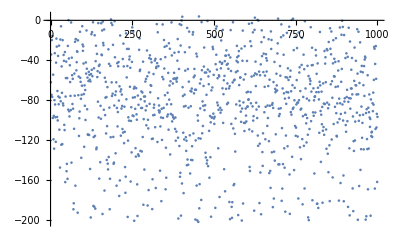

```mathematica
Table[

Module[{V,m1q,m2q,m3q,L1,L2,L3,L4,r1,r2,r3,r4,a1,a2,a3,b1,b2,b3,beta,cb,sb,n,p,v},
{m1q,m2q,m3q,L1,L2,L3,L4,r1,r2,r3,r4,a1,a2,a3,b1,b2,b3}=tunePara[c,(*{beta_,v_,n_,p_}*){beta=30.0°,v=1,n=10,p=10^-5}];
cb=Cos[beta];
sb=Sin[beta];

V=1/4 (k1^4 L1+k2^4 L1+4 k1^3 k2 L4-2 m3q vL^2+r1 vL^4-2 m3q vR^2+r3 vL^2 vR^2+r1 vR^4+k1^2 (2 k2^2 (L1+4 L2+2 L3)-2 m1q+a1 vL^2+2 b2 vL vR+a1 vR^2)+2 k1 k2 (2 k2^2 L4-4 m2q+2 a2 vL^2+b1 vL vR+2 a2 vR^2)+k2^2 (-2 m1q+a3 vL^2+2 b3 vL vR+a3 vR^2+a1 (vL^2+vR^2)));
(*{D[V,k1],D[V,k2],D[V,vR],D[V,vL]}/.{k1->v cb,k2->v sb,vR->n v,vL ->p v}//Print;*)
(D[D[V,{{k1,k2,vR,vL}}],{{k1,k2,vR,vL}}]/.{k1->v cb,k2->v sb,vR->n v,vL ->p v}//(*MatrixForm*)Eigenvalues//Min)
]
,{c,clist}]//ListPlot
```

## not all CP

```mathematica
ϵ=ⅈ PauliMatrix[2]
ϕ=DiagonalMatrix[{κ1,κ2 Exp[i θ2]}/√2];
ϕt=ϵ.ϕ.ϵ/.cRep;
ΔL=({{0, 0}, {(vL Exp[i θL])/(√2), 0}});
ΔR=({{0, 0}, {vR/(√2), 0}});

ct[m_]:=Transpose[m/.cRep];
cRep={i->-i};
```

{{0,1},{-1,0}}

```mathematica
ct[ΔL]
```

{{0,(ⅇ^(-i θL) vL)/(√2)},{0,0}}

```mathematica
computeProucts[];
V=computeV[];
V
```

β2 (-1/4 ⅇ^(-i θL) vL vR κ1^2-1/4 ⅇ^(i θL) vL vR κ1^2)+β1 (1/4 ⅇ^(i θ2-i θL) vL vR κ1 κ2+1/4 ⅇ^(-i θ2+i θL) vL vR κ1 κ2)+α2c (-1/2 ⅇ^(i θ2) vL^2 κ1 κ2-1/2 ⅇ^(-i θ2) vR^2 κ1 κ2)+α2 (-1/2 ⅇ^(-i θ2) vL^2 κ1 κ2-1/2 ⅇ^(i θ2) vR^2 κ1 κ2)+(vL^2/2+vR^2/2) α1 (κ1^2/2+κ2^2/2)+β3 (-1/4 ⅇ^(2 i θ2-i θL) vL vR κ2^2-1/4 ⅇ^(-2 i θ2+i θL) vL vR κ2^2)+α3 ((vL^2 κ2^2)/4+(vR^2 κ2^2)/4)+(κ1^2/2+κ2^2/2)^2 λ1+(ⅇ^(-2 i θ2) κ1^2 κ2^2+ⅇ^(2 i θ2) κ1^2 κ2^2) λ2+κ1^2 κ2^2 λ3+(-ⅇ^(-i θ2) κ1 κ2-ⅇ^(i θ2) κ1 κ2) (κ1^2/2+κ2^2/2) λ4-(κ1^2/2+κ2^2/2) μ1^2-(-ⅇ^(-i θ2) κ1 κ2-ⅇ^(i θ2) κ1 κ2) μ2^2-(vL^2/2+vR^2/2) μ3^2+(vL^4/4+vR^4/4) ρ1+1/4 vL^2 vR^2 ρ3

```mathematica
(*eq3={D[V,vR]==0,
D[V,κ1]==0,
D[V,κ2]==0}*)
```

```mathematica
(*Solve[eq3,{μ1^2->m1q,μ2^2->m2q,μ3^2}]*)
```

```mathematica
greekRep={α1->a1,α2->a2,α2c->a2c,α3->a3,β1->b1,β2->b2,β3->b3,
μ1^2->m1q,μ2^2->m2q,μ3^2->m3q,
ρ1->r1,ρ2->r2,ρ3->r3,ρ4->r4,
λ1->L1,λ2->L2,λ3->L3,λ4->L4,
κ1->k1,κ2->k2};
```

```mathematica
Vnormal=(V/.greekRep)/.{a2c->a2,i->ⅈ}//Simplify;
```

```mathematica
Vnormal=FullSimplify[Vnormal,And[θ2>0,θL>0]]
```

1/4 (k1^4 L1+k2^4 L1-2 m3q vL^2+r1 vL^4-2 m3q vR^2+r3 vL^2 vR^2+r1 vR^4+k1^2 (2 k2^2 (L1+2 L3)-2 m1q+a1 (vL^2+vR^2))+k2^2 (-2 m1q+(a1+a3) (vL^2+vR^2))+2 k2 (k1 (-2 ((k1^2+k2^2) L4-2 m2q+a2 (vL^2+vR^2)) Cos[θ2]+4 k1 k2 L2 Cos[2 θ2]+b1 vL vR Cos[θ2-θL])-b3 k2 vL vR Cos[2 θ2-θL])-2 b2 k1^2 vL vR Cos[θL])

```mathematica
eq3A={D[Vnormal,vR]==0,
D[Vnormal,k1]==0,
D[Vnormal,k2]==0}//Simplify;
eq3B={D[Vnormal,vL]==0,
D[Vnormal,θ2]==0,
D[Vnormal,θL]==0}//Simplify
```

{vL (a3 k2^2+a1 (k1^2+k2^2)+2 r1 vL^2+r3 vR^2)+b1 k1 k2 vR Cos[θ2-θL]==2 m3q vL+4 a2 k1 k2 vL Cos[θ2]+b3 k2^2 vR Cos[2 θ2-θL]+b2 k1^2 vR Cos[θL],k2 (2 k1 (k1^2 L4+k2^2 L4-2 m2q+a2 vL^2+a2 vR^2) Sin[θ2]-8 k1^2 k2 L2 Sin[2 θ2]+vL vR (-b1 k1 Sin[θ2-θL]+2 b3 k2 Sin[2 θ2-θL]))==0,vL vR (b1 k1 k2 Sin[θ2-θL]-b3 k2^2 Sin[2 θ2-θL]+b2 k1^2 Sin[θL])==0}

```mathematica
solA=Solve[eq3A,{m1q,m2q,m3q}]
```

{{m1q→-1/(2 (k1^2-k2^2))(-2 k1^4 L1+2 k2^4 L1-a1 k1^2 vL^2+a1 k2^2 vL^2+a3 k2^2 vL^2-a1 k1^2 vR^2+a1 k2^2 vR^2+a3 k2^2 vR^2+4 k1^3 k2 L4 Cos[θ2]-4 k1 k2^3 L4 Cos[θ2]-2 b3 k2^2 vL vR Cos[2 θ2-θL]+2 b2 k1^2 vL vR Cos[θL]),m2q→-1/(4 (-k1^2+k2^2))(-4 k1^3 k2 L3+4 k1 k2^3 L3-a3 k1 k2 vL^2-a3 k1 k2 vR^2+2 k1^4 L4 Cos[θ2]-2 k2^4 L4 Cos[θ2]+2 a2 k1^2 vL^2 Cos[θ2]-2 a2 k2^2 vL^2 Cos[θ2]+2 a2 k1^2 vR^2 Cos[θ2]-2 a2 k2^2 vR^2 Cos[θ2]-8 k1^3 k2 L2 Cos[2 θ2]+8 k1 k2^3 L2 Cos[2 θ2]-b1 k1^2 vL vR Cos[θ2-θL]+b1 k2^2 vL vR Cos[θ2-θL]+2 b3 k1 k2 vL vR Cos[2 θ2-θL]-2 b2 k1 k2 vL vR Cos[θL]) Sec[θ2],m3q→-1/(2 vR)(-a1 k1^2 vR-a1 k2^2 vR-a3 k2^2 vR-r3 vL^2 vR-2 r1 vR^3+4 a2 k1 k2 vR Cos[θ2]-b1 k1 k2 vL Cos[θ2-θL]+b3 k2^2 vL Cos[2 θ2-θL]+b2 k1^2 vL Cos[θL])}}

```mathematica
eq3B/.solA//Simplify
%//FullSimplify
```

{{((-vL^2+vR^2) (2 r1 vL vR-r3 vL vR-b1 k1 k2 Cos[θ2-θL]+b3 k2^2 Cos[2 θ2-θL]+b2 k1^2 Cos[θL]))/vR==0,1/(-k1^2+k2^2)k2 Sec[θ2] (-k1^2 k2 (k1^2 (8 L2-4 L3)+k2^2 (-8 L2+4 L3)-a3 (vL^2+vR^2)) Sin[θ2]+vL vR (k2 (b2 k1^2+2 b3 k1^2-b3 k2^2) Sin[θ2-θL]-b3 k2^3 Sin[3 θ2-θL]+k1 (b1 (k1^2-k2^2) Sin[θL]+b2 k1 k2 Sin[θ2+θL])))==0,vL vR (b1 k1 k2 Sin[θ2-θL]-b3 k2^2 Sin[2 θ2-θL]+b2 k1^2 Sin[θL])==0}}

{{1/vR(-vL+vR) (vL+vR) (2 r1 vL vR-r3 vL vR-b1 k1 k2 Cos[θ2-θL]+b3 k2^2 Cos[2 θ2-θL]+b2 k1^2 Cos[θL])==0,1/(-k1^2+k2^2)k2 (vL vR (2 b3 k2^3 Cos[2 θ2]+k1 (-2 b3 k1 k2+b1 (k1-k2) (k1+k2) Sec[θ2])) Sin[θL]+k2 (k1^2 (-4 (k1-k2) (k1+k2) (2 L2-L3)+a3 (vL^2+vR^2))+2 vL vR ((b2+b3) k1^2-b3 k2^2-b3 k2^2 Cos[2 θ2]) Cos[θL]) Tan[θ2])==0,vL vR (b1 k1 k2 Sin[θ2-θL]-b3 k2^2 Sin[2 θ2-θL]+b2 k1^2 Sin[θL])==0}}

```mathematica
eqBsimp={1/vR(-vL+vR) (vL+vR) (2 r1 vL vR-r3 vL vR-b1 k1 k2 Cos[θ2-θL]+b3 k2^2 Cos[2 θ2-θL]+b2 k1^2 Cos[θL])==0,1/(-k1^2+k2^2)k2 (vL vR (2 b3 k2^3 Cos[2 θ2]+k1 (-2 b3 k1 k2+b1 (k1-k2) (k1+k2) Sec[θ2])) Sin[θL]+k2 (k1^2 (-4 (k1-k2) (k1+k2) (2 L2-L3)+a3 (vL^2+vR^2))+2 vL vR ((b2+b3) k1^2-b3 k2^2-b3 k2^2 Cos[2 θ2]) Cos[θL]) Tan[θ2])==0,vL vR (b1 k1 k2 Sin[θ2-θL]-b3 k2^2 Sin[2 θ2-θL]+b2 k1^2 Sin[θL])==0};
```

```mathematica
Reduce[eqBsimp]
```

$Aborted

```mathematica
(vL vR (2 b3 k2^3 Cos[2 θ2]+k1 (-2 b3 k1 k2+b1 (k1-k2) (k1+k2) Sec[θ2])) Sin[θL]+k2 (k1^2 (-4 (k1-k2) (k1+k2) (2 L2-L3)+a3 (vL^2+vR^2))+2 vL vR ((b2+b3) k1^2-b3 k2^2-b3 k2^2 Cos[2 θ2]) Cos[θL]) Tan[θ2])Cos[θ2]//FullSimplify
```

k2 (k1^2 (-4 (k1-k2) (k1+k2) (2 L2-L3)+a3 (vL^2+vR^2))+2 vL vR ((b2+b3) k1^2-b3 k2^2-b3 k2^2 Cos[2 θ2]) Cos[θL]) Sin[θ2]+vL vR (b1 k1 (k1-k2) (k1+k2)+2 b3 k2 Cos[θ2] (-k1^2+k2^2 Cos[2 θ2])) Sin[θL]

```mathematica
eqBsimp/.{θ2->0,θL->0}//Simplify
```

{((-vL+vR) (vL+vR) (b2 k1^2-b1 k1 k2+b3 k2^2+2 r1 vL vR-r3 vL vR))/vR==0,True,True}

## CP (ϕt→-)

```mathematica
ϵ=ⅈ PauliMatrix[2];
cRep={i->-i};
ct[m_]:=Transpose[m/.cRep];

ϕ=DiagonalMatrix[{κ1,κ2 Exp[i t2]}/√2];
ϕt=-ϵ.ϕ.ϵ/.cRep;
ΔL=({{x2, x3}, {x1, -x2}})/.{x1->x1 Exp[i f1],x2->x2 Exp[i f2],x3->x3 Exp[i f3]};
ΔR=({{y2, y3}, {y1, -y2}})/.{y1->y1 Exp[i g1],y2->y2 Exp[i g2],y3->y3 Exp[i g3]};
```

```mathematica
ct[ΔL]
```

{{ⅇ^(-f2 i) x2,ⅇ^(-f1 i) x1},{ⅇ^(-f3 i) x3,-ⅇ^(-f2 i) x2}}

```mathematica
computeProucts[];
V=computeV[];
V
```

α2c (ⅇ^(i t2) (x1^2+2 x2^2+x3^2) κ1 κ2+ⅇ^(-i t2) (y1^2+2 y2^2+y3^2) κ1 κ2)+α2 (ⅇ^(-i t2) (x1^2+2 x2^2+x3^2) κ1 κ2+ⅇ^(i t2) (y1^2+2 y2^2+y3^2) κ1 κ2)+(x1^2+2 x2^2+x3^2+y1^2+2 y2^2+y3^2) α1 (κ1^2/2+κ2^2/2)+β3 (1/2 ⅇ^(f3 i-g3 i) x3 y3 κ1^2+1/2 ⅇ^(-f3 i+g3 i) x3 y3 κ1^2+ⅇ^(f2 i-g2 i-i t2) x2 y2 κ1 κ2+ⅇ^(-f2 i+g2 i+i t2) x2 y2 κ1 κ2+1/2 ⅇ^(f1 i-g1 i-2 i t2) x1 y1 κ2^2+1/2 ⅇ^(-f1 i+g1 i+2 i t2) x1 y1 κ2^2)+β1 (1/2 ⅇ^(f2 i-g2 i) x2 y2 κ1^2+1/2 ⅇ^(-f2 i+g2 i) x2 y2 κ1^2+1/2 ⅇ^(f1 i-g1 i-i t2) x1 y1 κ1 κ2+1/2 ⅇ^(-f1 i+g1 i+i t2) x1 y1 κ1 κ2+1/2 ⅇ^(-f3 i+g3 i-i t2) x3 y3 κ1 κ2+1/2 ⅇ^(f3 i-g3 i+i t2) x3 y3 κ1 κ2+1/2 ⅇ^(f2 i-g2 i) x2 y2 κ2^2+1/2 ⅇ^(-f2 i+g2 i) x2 y2 κ2^2)+α3 ((x2^2 κ1^2)/2+(x3^2 κ1^2)/2+(y2^2 κ1^2)/2+(y3^2 κ1^2)/2+(x1^2 κ2^2)/2+(x2^2 κ2^2)/2+(y1^2 κ2^2)/2+(y2^2 κ2^2)/2)+β2 (1/2 ⅇ^(f1 i-g1 i) x1 y1 κ1^2+1/2 ⅇ^(-f1 i+g1 i) x1 y1 κ1^2+ⅇ^(-f2 i+g2 i-i t2) x2 y2 κ1 κ2+ⅇ^(f2 i-g2 i+i t2) x2 y2 κ1 κ2+1/2 ⅇ^(-f3 i+g3 i-2 i t2) x3 y3 κ2^2+1/2 ⅇ^(f3 i-g3 i+2 i t2) x3 y3 κ2^2)+(κ1^2/2+κ2^2/2)^2 λ1+(ⅇ^(-2 i t2) κ1^2 κ2^2+ⅇ^(2 i t2) κ1^2 κ2^2) λ2+κ1^2 κ2^2 λ3+(ⅇ^(-i t2) κ1 κ2+ⅇ^(i t2) κ1 κ2) (κ1^2/2+κ2^2/2) λ4-(κ1^2/2+κ2^2/2) μ1^2-(ⅇ^(-i t2) κ1 κ2+ⅇ^(i t2) κ1 κ2) μ2^2-(x1^2+2 x2^2+x3^2+y1^2+2 y2^2+y3^2) μ3^2+((x1^2+2 x2^2+x3^2)^2+(y1^2+2 y2^2+y3^2)^2) ρ1+((2 ⅇ^(-2 f2 i) x2^2+2 ⅇ^(-f1 i-f3 i) x1 x3) (2 ⅇ^(2 f2 i) x2^2+2 ⅇ^(f1 i+f3 i) x1 x3)+(2 ⅇ^(-2 g2 i) y2^2+2 ⅇ^(-g1 i-g3 i) y1 y3) (2 ⅇ^(2 g2 i) y2^2+2 ⅇ^(g1 i+g3 i) y1 y3)) ρ2+(x1^2+2 x2^2+x3^2) (y1^2+2 y2^2+y3^2) ρ3+((2 ⅇ^(2 f2 i) x2^2+2 ⅇ^(f1 i+f3 i) x1 x3) (2 ⅇ^(-2 g2 i) y2^2+2 ⅇ^(-g1 i-g3 i) y1 y3)+(2 ⅇ^(-2 f2 i) x2^2+2 ⅇ^(-f1 i-f3 i) x1 x3) (2 ⅇ^(2 g2 i) y2^2+2 ⅇ^(g1 i+g3 i) y1 y3)) ρ4

```mathematica
r1
```

r1

```mathematica
greekRep={α1->a1,α2->a2,α2c->a2c,α3->a3,β1->b1,β2->b2,β3->b3,
μ1^2->m1q,μ2^2->m2q,μ3^2->m3q,
ρ1->r1,ρ2->r2,ρ3->r3,ρ4->r4,
λ1->L1,λ2->L2,λ3->L3,λ4->L4,
κ1->k1,κ2->k2};
```

```mathematica
Vnormal=(V/.greekRep)/.{a2c->a2,i->ⅈ}//Simplify;
```

```mathematica
Vnormal=FullSimplify[Vnormal,t2>f1>f2>f3>g1>g2>g3>0]
```

1/4 (k1^4 L1+k2^4 L1+2 k2^2 (-m1q+a3 (x1^2+x2^2+y1^2+y2^2)+a1 (x1^2+2 x2^2+x3^2+y1^2+2 y2^2+y3^2))+2 k1^2 (k2^2 (L1+2 L3)-m1q+a3 (x2^2+x3^2+y2^2+y3^2)+a1 (x1^2+2 x2^2+x3^2+y1^2+2 y2^2+y3^2))+4 (4 r2 x2^4+4 r2 x1^2 x3^2+r3 x1^2 y1^2+2 r3 x2^2 y1^2+r3 x3^2 y1^2+2 r3 x1^2 y2^2+4 r3 x2^2 y2^2+2 r3 x3^2 y2^2+4 r2 y2^4+(r3 (x1^2+2 x2^2+x3^2)+4 r2 y1^2) y3^2-m3q (x1^2+2 x2^2+x3^2+y1^2+2 y2^2+y3^2)+r1 ((x1^2+2 x2^2+x3^2)^2+(y1^2+2 y2^2+y3^2)^2)))+8 r2 x1 x2^2 x3 Cos[f1-2 f2+f3]+b2 k1^2 x1 y1 Cos[f1-g1]+8 r4 x2^2 y2^2 Cos[2 f2-2 g2]+8 r4 x1 x3 y2^2 Cos[f1+f3-2 g2]+b1 k1^2 x2 y2 Cos[f2-g2]+b1 k2^2 x2 y2 Cos[f2-g2]+b3 k1^2 x3 y3 Cos[f3-g3]+8 r4 x2^2 y1 y3 Cos[2 f2-g1-g3]+8 r4 x1 x3 y1 y3 Cos[f1+f3-g1-g3]+8 r2 y1 y2^2 y3 Cos[g1-2 g2+g3]+b3 k2^2 x1 y1 Cos[f1-g1-2 t2]+b1 k1 k2 x1 y1 Cos[f1-g1-t2]+2 b3 k1 k2 x2 y2 Cos[f2-g2-t2]+k1^3 k2 L4 Cos[t2]+k1 k2^3 L4 Cos[t2]-2 k1 k2 m2q Cos[t2]+2 a2 k1 k2 x1^2 Cos[t2]+4 a2 k1 k2 x2^2 Cos[t2]+2 a2 k1 k2 x3^2 Cos[t2]+2 a2 k1 k2 y1^2 Cos[t2]+4 a2 k1 k2 y2^2 Cos[t2]+2 a2 k1 k2 y3^2 Cos[t2]+2 k1^2 k2^2 L2 Cos[2 t2]+2 b2 k1 k2 x2 y2 Cos[f2-g2+t2]+b1 k1 k2 x3 y3 Cos[f3-g3+t2]+b2 k2^2 x3 y3 Cos[f3-g3+2 t2]

```mathematica
fieldLength={k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}//Length
cLength={m1q,m2q,m3q,L1,L2,L3,L4,r1,r2,r3,r4,a1,a2,a3,b1,b2,b3}//Length
```

15

17

```mathematica
Vstring=ToString[FortranForm[Vnormal]];
Vstring=StringReplace[Vstring,"Cos"->"cos"];
```

```mathematica
strList={
"def V(fields,couplings):",
"(k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3)=fields",
"(m1q,m2q,m3q,L1,L2,L3,L4,r1,r2,r3,r4,a1,a2,a3,b1,b2,b3)=couplings",
"return "<>Vstring
};
```

```mathematica
string="from math import cos \n"<>
"fieldLength="<>ToString[fieldLength]<>
"\n"<>
"cLength="<>ToString[cLength]<>
"\n";
Do[string=string<>str<>"\n\t",{str,strList}]
Export[NotebookDirectory[]<>"VfunCPV.py",string,"Text"]
```

D:\Dropbox\mywork\LR-scalar\code\VfunCPV.py

## CP x=xr+xi (useless)

```mathematica
ϵ=ⅈ PauliMatrix[2];
cRep={i->-i};
ct[m_]:=Transpose[m/.cRep];

ϕ=DiagonalMatrix[{κ1,κ2 }/√2]/.{κ1->k1,κ2->k2r+i k2i};
ϕt=ϵ.ϕ.ϵ/.cRep;
ΔL=({{x2, x3}, {x1, -x2}})/.{x1->x1r+i x1i,x2->x2r+i x2i ,x3->x3r+i x3i};
ΔR=({{y2, y3}, {y1, -y2}})/.{y1->y1r+i y1i,y2->y2r+i y2i,y3->y3r+i y3i};
```

```mathematica
ct[ΔL]
```

{{-i x2i+x2r,-i x1i+x1r},{-i x3i+x3r,i x2i-x2r}}

```mathematica
computeProucts[];
V=computeV[]//Simplify;
V
```

-1/2 (k1^2-i^2 k2i^2+k2r^2) (-x1r^2-2 x2r^2-x3r^2-y1r^2-2 y2r^2+i^2 (x1i^2+2 x2i^2+x3i^2+y1i^2+2 y2i^2+y3i^2)-y3r^2) α1+(-k1 (i k2i-k2r) (-x1r^2-2 x2r^2+i^2 (x1i^2+2 x2i^2+x3i^2)-x3r^2)+k1 (i k2i+k2r) (-y1r^2-2 y2r^2+i^2 (y1i^2+2 y2i^2+y3i^2)-y3r^2)) α2+(k1 (i k2i+k2r) (-x1r^2-2 x2r^2+i^2 (x1i^2+2 x2i^2+x3i^2)-x3r^2)-k1 (i k2i-k2r) (-y1r^2-2 y2r^2+i^2 (y1i^2+2 y2i^2+y3i^2)-y3r^2)) α2c+1/2 (i^4 k2i^2 (x1i^2+x2i^2+y1i^2+y2i^2)+k2r^2 (x1r^2+x2r^2+y1r^2+y2r^2)-i^2 (k2r^2 (x1i^2+x2i^2+y1i^2+y2i^2)+k2i^2 (x1r^2+x2r^2+y1r^2+y2r^2)+k1^2 (x2i^2+x3i^2+y2i^2+y3i^2))+k1^2 (x2r^2+x3r^2+y2r^2+y3r^2)) α3+(i^4 k2i^2 x2i y2i+k1^2 x2r y2r+k2r^2 x2r y2r+k1 k2r (x1r y1r+x3r y3r)-i^2 (k1^2 x2i y2i+k2r^2 x2i y2i+k2i^2 x2r y2r+k1 k2r (x1i y1i+x3i y3i)+k1 k2i (-x1r y1i+x1i y1r+x3r y3i-x3i y3r))) β1+(-k1^2 x1r y1r-2 k1 k2r x2r y2r+i^4 k2i^2 x3i y3i-k2r^2 x3r y3r+i^2 (k1^2 x1i y1i+2 k1 (k2r x2i y2i+k2i x2r y2i-k2i x2i y2r)+k2r^2 x3i y3i+2 k2i k2r x3r y3i-2 k2i k2r x3i y3r-k2i^2 x3r y3r)) β2+(i^4 k2i^2 x1i y1i-k2r^2 x1r y1r-2 k1 k2r x2r y2r+i^2 (k2r^2 x1i y1i-k2i^2 x1r y1r-2 k1 k2i x2r y2i+2 k2r (-k2i x1r y1i+k2i x1i y1r+k1 x2i y2i)+2 k1 k2i x2i y2r+k1^2 x3i y3i)-k1^2 x3r y3r) β3+1/4 (k1^2-i^2 k2i^2+k2r^2)^2 λ1+2 k1^2 (i^2 k2i^2+k2r^2) λ2+k1^2 (-i k2i+k2r) (i k2i+k2r) λ3-k1 k2r (k1^2-i^2 k2i^2+k2r^2) λ4-1/2 (k1^2-i^2 k2i^2+k2r^2) μ1^2+2 k1 k2r μ2^2+(-x1r^2-2 x2r^2-x3r^2-y1r^2-2 y2r^2+i^2 (x1i^2+2 x2i^2+x3i^2+y1i^2+2 y2i^2+y3i^2)-y3r^2) μ3^2+((x1r^2+2 x2r^2-i^2 (x1i^2+2 x2i^2+x3i^2)+x3r^2)^2+(y1r^2+2 y2r^2-i^2 (y1i^2+2 y2i^2+y3i^2)+y3r^2)^2) ρ1+(4 ((-i x2i+x2r)^2+(-i x1i+x1r) (-i x3i+x3r)) ((i x2i+x2r)^2+(i x1i+x1r) (i x3i+x3r))+4 ((-i y2i+y2r)^2+(-i y1i+y1r) (-i y3i+y3r)) ((i y2i+y2r)^2+(i y1i+y1r) (i y3i+y3r))) ρ2+(-x1r^2-2 x2r^2+i^2 (x1i^2+2 x2i^2+x3i^2)-x3r^2) (-y1r^2-2 y2r^2+i^2 (y1i^2+2 y2i^2+y3i^2)-y3r^2) ρ3+(4 ((i x2i+x2r)^2+(i x1i+x1r) (i x3i+x3r)) ((-i y2i+y2r)^2+(-i y1i+y1r) (-i y3i+y3r))+4 ((-i x2i+x2r)^2+(-i x1i+x1r) (-i x3i+x3r)) ((i y2i+y2r)^2+(i y1i+y1r) (i y3i+y3r))) ρ4

```mathematica
greekRep={α1->a1,α2->a2,α2c->a2c,α3->a3,β1->b1,β2->b2,β3->b3,
μ1^2->m1q,μ2^2->m2q,μ3^2->m3q,
ρ1->r1,ρ2->r2,ρ3->r3,ρ4->r4,
λ1->L1,λ2->L2,λ3->L3,λ4->L4,
κ1->k1,κ2->k2};
```

```mathematica
Vnormal=Simplify[Collect[(V/.greekRep)/.{a2c->a2},i],i^2==1];
```

```mathematica
Coefficient[Vnormal,i]
```

0

```mathematica
Vnormal=FullSimplify[Vnormal]
```

(k1^4 L1)/4-1/2 k1^2 k2i^2 L1+(k2i^4 L1)/4+1/2 k1^2 k2r^2 L1-1/2 k2i^2 k2r^2 L1+(k2r^4 L1)/4+2 k1^2 k2i^2 L2+2 k1^2 k2r^2 L2-k1^2 k2i^2 L3+k1^2 k2r^2 L3-k1^3 k2r L4+k1 k2i^2 k2r L4-k1 k2r^3 L4-(k1^2 m1q)/2+(k2i^2 m1q)/2-(k2r^2 m1q)/2+2 k1 k2r m2q+1/2 a1 k1^2 x1r^2-1/2 a1 k2i^2 x1r^2-2 a2 k1 k2r x1r^2+1/2 a1 k2r^2 x1r^2-m3q x1r^2+r1 x1r^4+4 r2 x2i^4+a1 k1^2 x2r^2-a1 k2i^2 x2r^2-4 a2 k1 k2r x2r^2+a1 k2r^2 x2r^2-2 m3q x2r^2+4 r1 x1r^2 x2r^2-8 r2 x2i^2 x2r^2+4 r1 x2r^4+4 r2 x2r^4+8 r2 x1i x2i^2 x3i-16 r2 x1r x2i x2r x3i+8 r2 x1i x2r^2 x3i+4 r2 x1i^2 x3i^2-4 r2 x1r^2 x3i^2+2 a2 k1 k2r (x1i^2+2 x2i^2+x3i^2)-2 r1 x1r^2 (x1i^2+2 x2i^2+x3i^2)-4 r1 x2r^2 (x1i^2+2 x2i^2+x3i^2)+r1 (x1i^2+2 x2i^2+x3i^2)^2+8 r2 x1r x2i^2 x3r-16 r2 x1i x2i x2r x3r+8 r2 x1r x2r^2 x3r+1/2 a1 k1^2 x3r^2-1/2 a1 k2i^2 x3r^2-2 a2 k1 k2r x3r^2+1/2 a1 k2r^2 x3r^2-m3q x3r^2-4 r2 x1i^2 x3r^2+2 r1 x1r^2 x3r^2+4 r2 x1r^2 x3r^2+4 r1 x2r^2 x3r^2-2 r1 (x1i^2+2 x2i^2+x3i^2) x3r^2+r1 x3r^4+b3 k2i^2 x1i y1i-b2 k1^2 x1r y1r-b3 k2r^2 x1r y1r+1/2 a1 k1^2 y1r^2-1/2 a1 k2i^2 y1r^2-2 a2 k1 k2r y1r^2+1/2 a1 k2r^2 y1r^2-m3q y1r^2+r3 x1r^2 y1r^2+2 r3 x2r^2 y1r^2-r3 (x1i^2+2 x2i^2+x3i^2) y1r^2+r3 x3r^2 y1r^2+r1 y1r^4+b1 k2i^2 x2i y2i+8 r4 x2i^2 y2i^2+8 r4 x2r^2 y2i^2+8 r4 x1i x3i y2i^2+8 r4 x1r x3r y2i^2+4 r2 y2i^4+1/2 a3 k2i^2 (x1i^2+x2i^2+y1i^2+y2i^2)+b1 k1^2 x2r y2r-2 b2 k1 k2r x2r y2r-2 b3 k1 k2r x2r y2r+b1 k2r^2 x2r y2r-32 r4 x2i x2r y2i y2r-16 r4 x1r x3i y2i y2r-16 r4 x1i x3r y2i y2r+a1 k1^2 y2r^2-a1 k2i^2 y2r^2-4 a2 k1 k2r y2r^2+a1 k2r^2 y2r^2-2 m3q y2r^2+2 r3 x1r^2 y2r^2+8 r4 x2i^2 y2r^2+4 r3 x2r^2 y2r^2+8 r4 x2r^2 y2r^2+8 r4 x1i x3i y2r^2-2 r3 (x1i^2+2 x2i^2+x3i^2) y2r^2+8 r4 x1r x3r y2r^2+2 r3 x3r^2 y2r^2+4 r1 y1r^2 y2r^2-8 r2 y2i^2 y2r^2+4 r1 y2r^4+4 r2 y2r^4+1/2 a3 k2r^2 (x1r^2+x2r^2+y1r^2+y2r^2)+b2 k2i^2 x3i y3i+8 r4 x2i^2 y1i y3i+8 r4 x2r^2 y1i y3i+8 r4 x1i x3i y1i y3i+8 r4 x1r x3r y1i y3i-16 r4 x2i x2r y1r y3i-8 r4 x1r x3i y1r y3i-8 r4 x1i x3r y1r y3i+8 r2 y1i y2i^2 y3i-16 r2 y1r y2i y2r y3i+8 r2 y1i y2r^2 y3i+4 r2 y1i^2 y3i^2-4 r2 y1r^2 y3i^2+b3 (k2r^2 x1i y1i+2 k2r (-k2i x1r y1i+k2i x1i y1r+k1 x2i y2i)-k2i (k2i x1r y1r+2 k1 x2r y2i-2 k1 x2i y2r)+k1^2 x3i y3i)+2 a2 k1 k2r (y1i^2+2 y2i^2+y3i^2)-r3 x1r^2 (y1i^2+2 y2i^2+y3i^2)-2 r3 x2r^2 (y1i^2+2 y2i^2+y3i^2)+r3 (x1i^2+2 x2i^2+x3i^2) (y1i^2+2 y2i^2+y3i^2)-r3 x3r^2 (y1i^2+2 y2i^2+y3i^2)-2 r1 y1r^2 (y1i^2+2 y2i^2+y3i^2)-4 r1 y2r^2 (y1i^2+2 y2i^2+y3i^2)+r1 (y1i^2+2 y2i^2+y3i^2)^2-1/2 a1 k1^2 (x1i^2+2 x2i^2+x3i^2+y1i^2+2 y2i^2+y3i^2)+1/2 a1 k2i^2 (x1i^2+2 x2i^2+x3i^2+y1i^2+2 y2i^2+y3i^2)-1/2 a1 k2r^2 (x1i^2+2 x2i^2+x3i^2+y1i^2+2 y2i^2+y3i^2)+m3q (x1i^2+2 x2i^2+x3i^2+y1i^2+2 y2i^2+y3i^2)-1/2 a3 (k2r^2 (x1i^2+x2i^2+y1i^2+y2i^2)+k2i^2 (x1r^2+x2r^2+y1r^2+y2r^2)+k1^2 (x2i^2+x3i^2+y2i^2+y3i^2))-b3 k1^2 x3r y3r-b2 k2r^2 x3r y3r-16 r4 x2i x2r y1i y3r-8 r4 x1r x3i y1i y3r-8 r4 x1i x3r y1i y3r+8 r4 x2i^2 y1r y3r+8 r4 x2r^2 y1r y3r+8 r4 x1i x3i y1r y3r+8 r4 x1r x3r y1r y3r+8 r2 y1r y2i^2 y3r-16 r2 y1i y2i y2r y3r+8 r2 y1r y2r^2 y3r+1/2 a1 k1^2 y3r^2-1/2 a1 k2i^2 y3r^2-2 a2 k1 k2r y3r^2+1/2 a1 k2r^2 y3r^2-m3q y3r^2+r3 x1r^2 y3r^2+2 r3 x2r^2 y3r^2-r3 (x1i^2+2 x2i^2+x3i^2) y3r^2+r3 x3r^2 y3r^2-4 r2 y1i^2 y3r^2+2 r1 y1r^2 y3r^2+4 r2 y1r^2 y3r^2+4 r1 y2r^2 y3r^2-2 r1 (y1i^2+2 y2i^2+y3i^2) y3r^2+r1 y3r^4+b1 k1 k2r (x1r y1r+x3r y3r)+b2 (k1^2 x1i y1i+2 k1 (k2r x2i y2i+k2i x2r y2i-k2i x2i y2r)+k2r (k2r x3i+2 k2i x3r) y3i-k2i (2 k2r x3i+k2i x3r) y3r)+1/2 a3 k1^2 (x2r^2+x3r^2+y2r^2+y3r^2)-b1 (k1^2 x2i y2i+k2r^2 x2i y2i+k2i^2 x2r y2r+k1 k2r (x1i y1i+x3i y3i)+k1 k2i (-x1r y1i+x1i y1r+x3r y3i-x3i y3r))

```mathematica
fieldLength={k1,k2r,k2i,x1r,x1i,x2r,x2i,x3r,x3i,y1r,y1i,y2r,y2i,y3r,y3i}//Length
cLength={m1q,m2q,m3q,L1,L2,L3,L4,r1,r2,r3,r4,a1,a2,a3,b1,b2,b3}//Length
```

15

17

```mathematica
Vstring=ToString[FortranForm[Vnormal]];
Vstring
```

(k1**4*L1)/4. - (k1**2*k2i**2*L1)/2. + (k2i**4*L1)/4. + (k1**2*k2r**2*L1)/2. - (k2i**2*k2r**2*L1)/2. + (k2r**4*L1)/4. + 2*k1**2*k2i**2*L2 + 2*k1**2*k2r**2*L2 - k1**2*k2i**2*L3 + k1**2*k2r**2*L3 - k1**3*k2r*L4 + k1*k2i**2*k2r*L4 - k1*k2r**3*L4 - (k1**2*m1q)/2. + (k2i**2*m1q)/2. - (k2r**2*m1q)/2. + 2*k1*k2r*m2q + (a1*k1**2*x1r**2)/2. - (a1*k2i**2*x1r**2)/2. - 2*a2*k1*k2r*x1r**2 + (a1*k2r**2*x1r**2)/2. - m3q*x1r**2 + r1*x1r**4 + 4*r2*x2i**4 + a1*k1**2*x2r**2 - a1*k2i**2*x2r**2 - 4*a2*k1*k2r*x2r**2 + a1*k2r**2*x2r**2 - 2*m3q*x2r**2 + 4*r1*x1r**2*x2r**2 - 8*r2*x2i**2*x2r**2 + 4*r1*x2r**4 + 4*r2*x2r**4 + 8*r2*x1i*x2i**2*x3i - 16*r2*x1r*x2i*x2r*x3i + 8*r2*x1i*x2r**2*x3i + 4*r2*x1i**2*x3i**2 - 4*r2*x1r**2*x3i**2 + 2*a2*k1*k2r*(x1i**2 + 2*x2i**2 + x3i**2) - 2*r1*x1r**2*(x1i**2 + 2*x2i**2 + x3i**2) - 4*r1*x2r**2*(x1i**2 + 2*x2i**2 + x3i**2) + r1*(x1i**2 + 2*x2i**2 + x3i**2)**2 + 8*r2*x1r*x2i**2*x3r - 16*r2*x1i*x2i*x2r*x3r + 8*r2*x1r*x2r**2*x3r + (a1*k1**2*x3r**2)/2. - (a1*k2i**2*x3r**2)/2. - 2*a2*k1*k2r*x3r**2 + (a1*k2r**2*x3r**2)/2. - m3q*x3r**2 - 4*r2*x1i**2*x3r**2 + 2*r1*x1r**2*x3r**2 + 4*r2*x1r**2*x3r**2 + 4*r1*x2r**2*x3r**2 - 2*r1*(x1i**2 + 2*x2i**2 + x3i**2)*x3r**2 + r1*x3r**4 + b3*k2i**2*x1i*y1i - b2*k1**2*x1r*y1r - b3*k2r**2*x1r*y1r + (a1*k1**2*y1r**2)/2. - (a1*k2i**2*y1r**2)/2. - 2*a2*k1*k2r*y1r**2 + (a1*k2r**2*y1r**2)/2. - m3q*y1r**2 + r3*x1r**2*y1r**2 + 2*r3*x2r**2*y1r**2 - r3*(x1i**2 + 2*x2i**2 + x3i**2)*y1r**2 + r3*x3r**2*y1r**2 + r1*y1r**4 + b1*k2i**2*x2i*y2i + 8*r4*x2i**2*y2i**2 + 8*r4*x2r**2*y2i**2 + 8*r4*x1i*x3i*y2i**2 + 8*r4*x1r*x3r*y2i**2 + 4*r2*y2i**4 + (a3*k2i**2*(x1i**2 + x2i**2 + y1i**2 + y2i**2))/2. + b1*k1**2*x2r*y2r - 2*b2*k1*k2r*x2r*y2r - 2*b3*k1*k2r*x2r*y2r + b1*k2r**2*x2r*y2r - 32*r4*x2i*x2r*y2i*y2r - 16*r4*x1r*x3i*y2i*y2r - 16*r4*x1i*x3r*y2i*y2r + a1*k1**2*y2r**2 - a1*k2i**2*y2r**2 - 4*a2*k1*k2r*y2r**2 + a1*k2r**2*y2r**2 - 2*m3q*y2r**2 + 2*r3*x1r**2*y2r**2 + 8*r4*x2i**2*y2r**2 + 4*r3*x2r**2*y2r**2 + 8*r4*x2r**2*y2r**2 + 8*r4*x1i*x3i*y2r**2 - 2*r3*(x1i**2 + 2*x2i**2 + x3i**2)*y2r**2 + 8*r4*x1r*x3r*y2r**2 + 2*r3*x3r**2*y2r**2 + 4*r1*y1r**2*y2r**2 - 8*r2*y2i**2*y2r**2 + 4*r1*y2r**4 + 4*r2*y2r**4 + (a3*k2r**2*(x1r**2 + x2r**2 + y1r**2 + y2r**2))/2. + b2*k2i**2*x3i*y3i + 8*r4*x2i**2*y1i*y3i + 8*r4*x2r**2*y1i*y3i + 8*r4*x1i*x3i*y1i*y3i + 8*r4*x1r*x3r*y1i*y3i - 16*r4*x2i*x2r*y1r*y3i - 8*r4*x1r*x3i*y1r*y3i - 8*r4*x1i*x3r*y1r*y3i + 8*r2*y1i*y2i**2*y3i - 16*r2*y1r*y2i*y2r*y3i + 8*r2*y1i*y2r**2*y3i + 4*r2*y1i**2*y3i**2 - 4*r2*y1r**2*y3i**2 + b3*(k2r**2*x1i*y1i + 2*k2r*(-(k2i*x1r*y1i) + k2i*x1i*y1r + k1*x2i*y2i) - k2i*(k2i*x1r*y1r + 2*k1*x2r*y2i - 2*k1*x2i*y2r) + k1**2*x3i*y3i) + 2*a2*k1*k2r*(y1i**2 + 2*y2i**2 + y3i**2) - r3*x1r**2*(y1i**2 + 2*y2i**2 + y3i**2) - 2*r3*x2r**2*(y1i**2 + 2*y2i**2 + y3i**2) + r3*(x1i**2 + 2*x2i**2 + x3i**2)*(y1i**2 + 2*y2i**2 + y3i**2) - r3*x3r**2*(y1i**2 + 2*y2i**2 + y3i**2) - 2*r1*y1r**2*(y1i**2 + 2*y2i**2 + y3i**2) - 4*r1*y2r**2*(y1i**2 + 2*y2i**2 + y3i**2) + r1*(y1i**2 + 2*y2i**2 + y3i**2)**2 - (a1*k1**2*(x1i**2 + 2*x2i**2 + x3i**2 + y1i**2 + 2*y2i**2 + y3i**2))/2. + (a1*k2i**2*(x1i**2 + 2*x2i**2 + x3i**2 + y1i**2 + 2*y2i**2 + y3i**2))/2. - (a1*k2r**2*(x1i**2 + 2*x2i**2 + x3i**2 + y1i**2 + 2*y2i**2 + y3i**2))/2. + m3q*(x1i**2 + 2*x2i**2 + x3i**2 + y1i**2 + 2*y2i**2 + y3i**2) - (a3*(k2r**2*(x1i**2 + x2i**2 + y1i**2 + y2i**2) + k2i**2*(x1r**2 + x2r**2 + y1r**2 + y2r**2) + k1**2*(x2i**2 + x3i**2 + y2i**2 + y3i**2)))/2. - b3*k1**2*x3r*y3r - b2*k2r**2*x3r*y3r - 16*r4*x2i*x2r*y1i*y3r - 8*r4*x1r*x3i*y1i*y3r - 8*r4*x1i*x3r*y1i*y3r + 8*r4*x2i**2*y1r*y3r + 8*r4*x2r**2*y1r*y3r + 8*r4*x1i*x3i*y1r*y3r + 8*r4*x1r*x3r*y1r*y3r + 8*r2*y1r*y2i**2*y3r - 16*r2*y1i*y2i*y2r*y3r + 8*r2*y1r*y2r**2*y3r + (a1*k1**2*y3r**2)/2. - (a1*k2i**2*y3r**2)/2. - 2*a2*k1*k2r*y3r**2 + (a1*k2r**2*y3r**2)/2. - m3q*y3r**2 + r3*x1r**2*y3r**2 + 2*r3*x2r**2*y3r**2 - r3*(x1i**2 + 2*x2i**2 + x3i**2)*y3r**2 + r3*x3r**2*y3r**2 - 4*r2*y1i**2*y3r**2 + 2*r1*y1r**2*y3r**2 + 4*r2*y1r**2*y3r**2 + 4*r1*y2r**2*y3r**2 - 2*r1*(y1i**2 + 2*y2i**2 + y3i**2)*y3r**2 + r1*y3r**4 + b1*k1*k2r*(x1r*y1r + x3r*y3r) + b2*(k1**2*x1i*y1i + 2*k1*(k2r*x2i*y2i + k2i*x2r*y2i - k2i*x2i*y2r) + k2r*(k2r*x3i + 2*k2i*x3r)*y3i - k2i*(2*k2r*x3i + k2i*x3r)*y3r) + (a3*k1**2*(x2r**2 + x3r**2 + y2r**2 + y3r**2))/2. - b1*(k1**2*x2i*y2i + k2r**2*x2i*y2i + k2i**2*x2r*y2r + k1*k2r*(x1i*y1i + x3i*y3i) + k1*k2i*(-(x1r*y1i) + x1i*y1r + x3r*y3i - x3i*y3r))

```mathematica
strList={
"def V(fields,couplings):",
"(k1,k2r,k2i,x1r,x1i,x2r,x2i,x3r,x3i,y1r,y1i,y2r,y2i,y3r,y3i)=fields",
"(m1q,m2q,m3q,L1,L2,L3,L4,r1,r2,r3,r4,a1,a2,a3,b1,b2,b3)=couplings",
"return "<>Vstring
};
```

```mathematica
string=
"fieldLength="<>ToString[fieldLength]<>
"\n"<>
"cLength="<>ToString[cLength]<>
"\n";
Do[string=string<>str<>"\n\t",{str,strList}]
Export[NotebookDirectory[]<>"VfunCPVri.py",string,"Text"]
```

D:\Dropbox\mywork\LR-scalar\code\VfunCPVri.py